```mathematica
(*
 * Gourav Siddhad
* Btech Computer Sc. 2nd Yr
* 3235
 *)
BisectionMethod[ao_,bo_,n_,f_] :=
Module[{},a=N[ao];b=N[bo];m=(a+b)/2;i=0;

If[f[a]*f[b]>0,
Print["We Can't Continue With Bisection Method As "f"(a)."f,"(b)>=0"];
	Return[]];

OutputDetails={{i,a,b,m,f[m]}};

While[i<n,
If[Sign[f[a]]==Sign[f[m]],a=m,b=m];
m=(a+b)/2;
i++;
OutputDetails=Append[OutputDetails,{i,a,b,m,f[m]}];];

Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","mi","F[mi]"}}],8]];
Print[" Root After ",n," Iterations : ",NumberForm[m,8]];
];
```

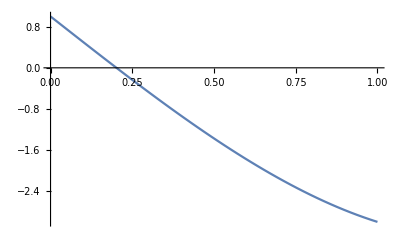

i | a | b | m | f[m]
0 | 0. | 1. | 0.5 | -1.375
1 | 0. | 0.5 | 0.25 | -0.234375
2 | 0. | 0.25 | 0.125 | 0.37695313
3 | 0.125 | 0.25 | 0.1875 | 0.069091797
4 | 0.1875 | 0.25 | 0.21875 | -0.083282471
5 | 0.1875 | 0.21875 | 0.203125 | -0.0072441101
6 | 0.1875 | 0.203125 | 0.1953125 | 0.030888081
7 | 0.1953125 | 0.203125 | 0.19921875 | 0.011812866
8 | 0.19921875 | 0.203125 | 0.20117188 | 0.0022820756
9 | 0.20117188 | 0.203125 | 0.20214844 | -0.0024815956
10 | 0.20117188 | 0.20214844 | 0.20166016 | -0.000099904253

Root After N Iterations 0.20166016

```mathematica
(* Example 1 *)
f[x_]:=x^3-5*x+1;
Plot[f[x],{x,0,1 }]
BisectionMethod[0,1,10,f]
```

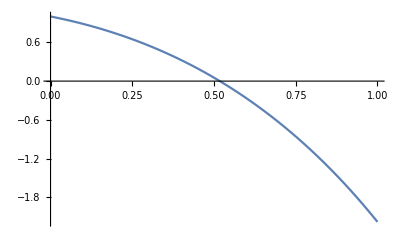

i | ai | bi | mi | F[mi]
0 | 0. | 1. | 0.5 | 0.053221927
1 | 0.5 | 1. | 0.75 | -0.85606114
2 | 0.5 | 0.75 | 0.625 | -0.3566906
3 | 0.5 | 0.625 | 0.5625 | -0.14129375
4 | 0.5 | 0.5625 | 0.53125 | -0.041512212
5 | 0.5 | 0.53125 | 0.515625 | 0.0064753408
6 | 0.515625 | 0.53125 | 0.5234375 | -0.017362025
7 | 0.515625 | 0.5234375 | 0.51953125 | -0.0054044018
8 | 0.515625 | 0.51953125 | 0.51757813 | 0.00054518442
9 | 0.51757813 | 0.51953125 | 0.51855469 | -0.0024271775
10 | 0.51757813 | 0.51855469 | 0.51806641 | -0.00094038902

Root After 10 Iterations : 0.51806641

```mathematica
(* Example 2 *)
f[x_]:=Cos[x]-x*ⅇ^x
Plot[f[x],{x,0,1}]
BisectionMethod[0,1,10,f]
```

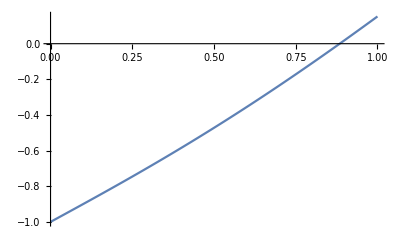

i | ai | bi | mi | F[mi]
0 | 0. | 1. | 0.5 | -0.47211745
1 | 0.5 | 1. | 0.75 | -0.17207308
2 | 0.75 | 1. | 0.875 | -0.012388199
3 | 0.875 | 1. | 0.9375 | 0.069593407
4 | 0.875 | 0.9375 | 0.90625 | 0.028435895
5 | 0.875 | 0.90625 | 0.890625 | 0.0079812284
6 | 0.875 | 0.890625 | 0.8828125 | -0.0022142544
7 | 0.8828125 | 0.890625 | 0.88671875 | 0.0028808088
8 | 0.8828125 | 0.88671875 | 0.88476563 | 0.00033260588
9 | 0.8828125 | 0.88476563 | 0.88378906 | -0.00094099231
10 | 0.88378906 | 0.88476563 | 0.88427734 | -0.0003042352

Root After 10 Iterations : 0.88427734

```mathematica
(* Example 3 *)
f[x_]:=Log[1+x]-Cos[x]
Plot[f[x],{x,0,1}]
BisectionMethod[0,1,10,f]
```

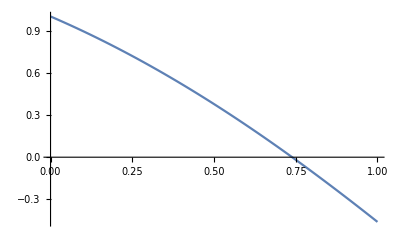

i | ai | bi | mi | F[mi]
0 | 0. | 1. | 0.5 | 0.37758256
1 | 0.5 | 1. | 0.75 | -0.018311131
2 | 0.5 | 0.75 | 0.625 | 0.18596312
3 | 0.625 | 0.75 | 0.6875 | 0.085334946
4 | 0.6875 | 0.75 | 0.71875 | 0.033879372
5 | 0.71875 | 0.75 | 0.734375 | 0.0078747255
6 | 0.734375 | 0.75 | 0.7421875 | -0.0051957117
7 | 0.734375 | 0.7421875 | 0.73828125 | 0.0013451498
8 | 0.73828125 | 0.7421875 | 0.74023438 | -0.0019238728
9 | 0.73828125 | 0.74023438 | 0.73925781 | -0.00028900915
10 | 0.73828125 | 0.73925781 | 0.73876953 | 0.00052815843

Root After 10 Iterations : 0.73876953

```mathematica
(* Example 4 *)
f[x_]:=Cos[x]-x
Plot[f[x],{x,0,1}]
BisectionMethod[0,1,10,f]
```

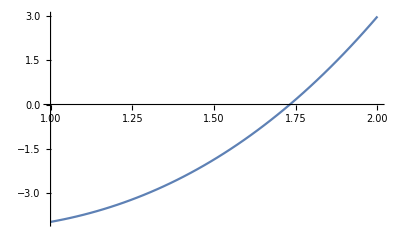

i | ai | bi | mi | F[mi]
0 | 1. | 2. | 1.5 | -1.875
1 | 1.5 | 2. | 1.75 | 0.171875
2 | 1.5 | 1.75 | 1.625 | -0.94335938
3 | 1.625 | 1.75 | 1.6875 | -0.40942383
4 | 1.6875 | 1.75 | 1.71875 | -0.12478638
5 | 1.71875 | 1.75 | 1.734375 | 0.022029877
6 | 1.71875 | 1.734375 | 1.7265625 | -0.051755428
7 | 1.7265625 | 1.734375 | 1.7304688 | -0.014957249
8 | 1.7304688 | 1.734375 | 1.7324219 | 0.0035126731
9 | 1.7304688 | 1.7324219 | 1.7314453 | -0.0057281954
10 | 1.7314453 | 1.7324219 | 1.7319336 | -0.0011092384

Root After 10 Iterations : 1.7319336

```mathematica
(* Example 5 *)
f[x_]:=x^3+x^2-3x-3
Plot[f[x],{x,1,2}]
BisectionMethod[1,2,10,f]
```

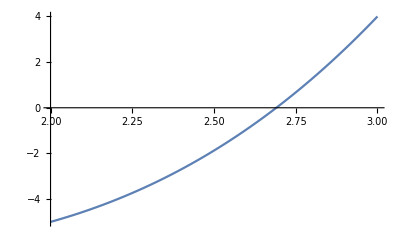

i | ai | bi | mi | F[mi]
0 | 2. | 3. | 2.5 | -1.875
1 | 2.5 | 3. | 2.75 | 0.671875
2 | 2.5 | 2.75 | 2.625 | -0.69335938
3 | 2.625 | 2.75 | 2.6875 | -0.034423828
4 | 2.6875 | 2.75 | 2.71875 | 0.31271362
5 | 2.6875 | 2.71875 | 2.703125 | 0.13765335
6 | 2.6875 | 2.703125 | 2.6953125 | 0.051243305
7 | 2.6875 | 2.6953125 | 2.6914063 | 0.0083170533
8 | 2.6875 | 2.6914063 | 2.6894531 | -0.013076536
9 | 2.6894531 | 2.6914063 | 2.6904297 | -0.0023855316
10 | 2.6904297 | 2.6914063 | 2.690918 | 0.002964313

Root After 10 Iterations : 2.690918

```mathematica
(* Example 6 *)
f[x_]:=x^3-2*x^2-5
Plot[f[x],{x,2,3}]
BisectionMethod[2,3,10,f]
```

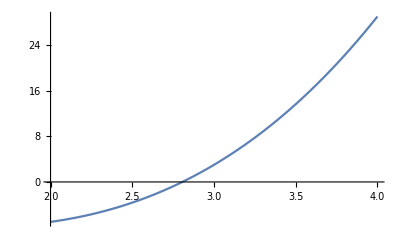

i | ai | bi | mi | F[mi]
0 | 2. | 3. | 2.5 | -3.625
1 | 2.5 | 3. | 2.75 | -0.765625
2 | 2.75 | 3. | 2.875 | 0.99804688
3 | 2.75 | 2.875 | 2.8125 | 0.087158203
4 | 2.75 | 2.8125 | 2.78125 | -0.34640503
5 | 2.78125 | 2.8125 | 2.796875 | -0.13142776
6 | 2.796875 | 2.8125 | 2.8046875 | -0.022587299
7 | 2.8046875 | 2.8125 | 2.8085938 | 0.032172143
8 | 2.8046875 | 2.8085938 | 2.8066406 | 0.0047641173
9 | 2.8046875 | 2.8066406 | 2.8056641 | -0.0089186644
10 | 2.8056641 | 2.8066406 | 2.8061523 | -0.0020790423

Root After 10 Iterations : 2.8061523

```mathematica
(* Example 7 *)
f[x_]:=x^3-x^2-4*x-3
Plot[f[x],{x,2,4}]
BisectionMethod[2,3,10,f]
```